# Fancy Spring Thing

### 3D Springdulum

We are going to do this two ways:

Getting the computer to do the derivatives and balance the forces.

Using the Lagrangian

### 1. Making the Computer Work

Consider a mass m hanging from a linear spring fixed to a pivot on the ceiling.  Use the standard spherical coordinate system (centered at the pivot) from Calculus to describe the position of the mass! If the natural length of the spring is L and the extension of the spring is “x” then the position of the mass is  
	(x+L)u[θ,ϕ]
where u[θ,ϕ]={ Cos[θ]Sin[ϕ], Sin[θ]Sin[ϕ], Cos[ϕ]} is the unit vector 
	Some of the possible motions are easy to describe.  Swinging side to side is ϕ changing. Swinging round and round is θ changing. Bobbing up and down is x changing.

We want to build the appropriate dynamical equations for the complicated coupled motion!  The only forces are gravity “vertical” 
	m g{0,0,-1} 
and the tension T acting along the spring so  
	±T{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]} 
As before the tension is proportional to how much the spring is stretched so T=k x.  We know that Newton discovered that F=m a so we have a set of three second order ODEs for the there DOFs

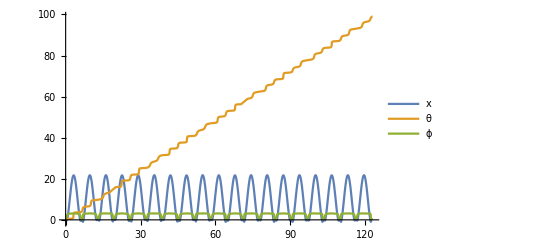

```mathematica
Clear[u,θ,ϕ,x,t,m,k,L,g]
u[θ_,ϕ_]:={ Cos[θ]Sin[ϕ], Sin[θ]Sin[ϕ], Cos[ϕ]}
{m,k,L,g}={1,1,1.2,9.8};
NewtonEqs=m g {0,0,-1}-k x[t]*u[θ[t],ϕ[t]]== m D[(x[t]+L)*u[θ[t],ϕ[t]],{t,2}];
TMax=123;
{xSol,θSol,ϕSol}=NDSolveValue[
{NewtonEqs, x[0]==0.1,x'[0]==0.2,θ[0]==0.3,θ'[0]==0.4,ϕ[0]==0.5,ϕ'[0]==0.6},
{x,θ,ϕ},{t,0, TMax}];
Plot[{xSol[t],θSol[t],ϕSol[t]},{t, 0, TMax},
PlotLegends->{"x","θ","ϕ"}]
```

### 2. Doing Some of the work for the computer

The kinetic energy is just 1/2 m ||v(||)^2 which is 
	1/2 m(x'[t]^2+(x[t]+L)^2(??θ'[t]^2+ϕ'[t]^2))
The potential energy is just the gravitational potential plus the sprint potential
	-m g (x[t]+L)Cos[ϕ]+1/2 k x^2.

```mathematica
Clear[Lagrange,m,k,L]
Lagrange[{x_,θ_,ϕ_}, {vx_,vθ_,vϕ_}]:=0.5  m (vx^2+ (x+L)^2(Sin[ϕ]^2 vθ^2+vϕ^2))+ m g (x+L) Cos[ϕ] - 0.5 k x^2 
DxL[{x_,θ_,ϕ_}, {vx_,vθ_,vϕ_}]=D[Lagrange[{x,θ,ϕ}, {vx,vθ,vϕ}],{{x,θ,ϕ}}];
DvL[{x_,θ_,ϕ_}, {vx_,vθ_,vϕ_}]=D[Lagrange[{x,θ,ϕ}, {vx,vθ,vϕ}],{{vx,vθ,vϕ}}];
LagrangeStuff= DxL[{x[t],θ[t],ϕ[t]},{vx[t],vθ[t],vϕ[t]}] -D[DvL[{x[t],θ[t],ϕ[t]},{vx[t],vθ[t],vϕ[t]}], t];
```

To solve as a first order system we need to add the “boring” equations.

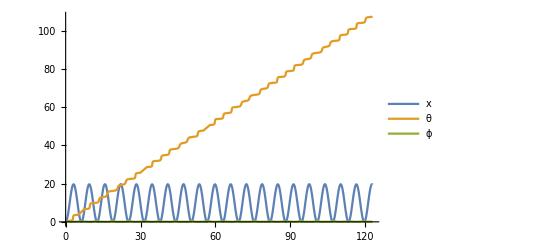

```mathematica
LagrangeFirstOrder= Join[
Table[ LagrangeStuff⟦i⟧==0,{i,1,3}],
{vx[t]==x'[t],vθ[t]==θ'[t],vϕ[t]==ϕ'[t]}];
{m,k,L,g}={1,1,1.2,9.8}; TMax=123;
{xSol,θSol,ϕSol,vxSol,vθSol,vϕSol}=NDSolveValue[
{LagrangeFirstOrder, x[0]==0.1,vx[0]==0.2,θ[0]==0.3,vθ[0]==0.4,ϕ[0]==0.5,vϕ[0]==0.6},
{x,θ,ϕ,vx,vθ,vϕ},{t,0, TMax}];
Plot[{xSol[t],θSol[t],ϕSol[t]},{t, 0, TMax},
PlotLegends->{"x","θ","ϕ"}]
```

If you do not like the conversion to a first order system then we can get rid of the extra function as follows.

```mathematica
LagrangeSecondOrder=LagrangeStuff/.{vx->x',vθ->θ',vϕ->ϕ'};
{m,k,L,g}={1,1,1.2,9.8}; TMax=123;
{xSol,θSol,ϕSol}=NDSolveValue[
{LagrangeSecondOrder=={0,0,0}, x[0]==0.1,x'[0]==0.2,θ[0]==0.3,θ'[0]==0.4,ϕ[0]==0.5,ϕ'[0]==0.6},
{x,θ,ϕ},{t,0, TMax}];
Plot[{xSol[t],θSol[t],ϕSol[t]},{t, 0, TMax},
PlotLegends->{"x","θ","ϕ"}]
```

-Graphics-